Reconstruct_Bullet.nb

A 3D volume of a bullet is reconstructed from neutron attenuation images acquired a the Paul Scherrer Institute neutron imaging facility.  An advanced neutron detector was developed by the University of California at Berkeley Space Sciences Laboratory.
The detector and neutron imaging are described in A.S. Tremsin, J.B. McPhate, J.V. Vallerga, O.H.W. Siegmund, W.B. Feller, E. Lehmann, L.G. Butler, M. Dawson, “High-resolution neutron microtomography with noiseless neutron counting detector”, Nucl. Instr. Meth. A, 652 (2011) 400-403.

1. Initialization:  Sets image size, paths, 
2. Attenuation:  All attenuation images are calculated from the raw images, including flat field normalization.  Two images are defective, and are replaced with the average of adjacent images.
3. Sinogram: All sinograms are created.
4. Centering:
5. Reconstruction:
6. Volume:

The program reads raw data images (text files), computes attenuation images (replaces two images), creates sinograms, explores sinogram centering, reconstructs slices, and assembles a volume.

## Step 1: Initialization

### 1.a Image size, Paths

```mathematica
ClearAll["Global`*"]
pathRoot = "/melete-nas01/lsu/scratch/BulletData/"
```

/melete-nas01/lsu/scratch/BulletData/

```mathematica
NX =256; NY=256;
```

```mathematica
NotebookDirectory[]
$OperatingSystem
$HomeDirectory
```

/Users/tomo3/Github/LSU-VisTrails/

Unix

/home/lbutler

```mathematica
DirectoryQ[pathRawData =  pathRoot<>"raw_bullet_images/"]
DirectoryQ[pathFigures =  pathRoot<>"figures/"]
DirectoryQ[pathAttenuation =  pathRoot<>"attenuation/"]
DirectoryQ[pathSinograms =  pathRoot<>"sinograms/"]
DirectoryQ[pathSlices=  pathRoot<>"slices/"]
DirectoryQ[pathVolumes=  pathRoot<>"volumes/"]
```

True

True

True

«3 more identical outputs»

### 1.b Define image processing functions

funcFilterRawImages[raw_]
In a high radiation environment, even if shielded from the main radiation beam, a detector can be damaged at the the pixel level. ONe strategy is to replace the bad pixel with an average of its neighbors.

```mathematica
funcFilterRawImages[raw_]:=Module[{anyZeros,filtered,r,c,medianFiltered},
filtered=raw;
anyZeros= Position[raw, p_?(#≤0 &)];
medianFiltered = MedianFilter[raw,1];
If[Length[anyZeros]>0,Module[{}, 
For[i=1,i<=Length[anyZeros],i++,
{r,c}=anyZeros[[i]];
filtered[[r,c]] = medianFiltered[[r,c]];  ]]];
filtered];
```

### 1.c DumpSave

```mathematica
DumpSave[pathRoot<>"step_1.mx",{NX, NY,pathRoot, pathAttenuation,pathFigures,pathRawData,pathSinograms,pathSlices,pathVolumes, funcFilterRawImages}]
ClearAll["Global`*"]
```

{256,256,/melete-nas01/lsu/scratch/BulletData/,/melete-nas01/lsu/scratch/BulletData/attenuation/,/melete-nas01/lsu/scratch/BulletData/figures/,/melete-nas01/lsu/scratch/BulletData/raw_bullet_images/,/melete-nas01/lsu/scratch/BulletData/sinograms/,/melete-nas01/lsu/scratch/BulletData/slices/,/melete-nas01/lsu/scratch/BulletData/volumes/,funcFilterRawImages}

## Step 2. Attenuation at the first rotation angle

```mathematica
pathRoot = "/melete-nas01/lsu/scratch/BulletData/"
Get[pathRoot<>"step_1.mx"]
```

/melete-nas01/lsu/scratch/BulletData/

### 2.a Open Beam

```mathematica
openBeam = Import[pathRawData<>"OpenBeam_600s","Table"];
openBeam=funcFilterRawImages[openBeam];
{Dimensions[openBeam],Min[openBeam],Mean[Flatten[openBeam]],Max[openBeam]}//N
(*gOpenBeam = ArrayPlot[openBeam, ImageSize->200]*)
```

{{256.,256.},4.,56751.6,123188.}

### 2.b Dark

```mathematica
dark =Import[pathRawData<>"DarkImage_FastShutterClosed_100s","Table"];
dark=funcFilterRawImages[dark];
{Dimensions[dark],Min[dark],Mean[Flatten[dark]],Max[dark]}//N
(*gDark = ArrayPlot[dark, ImageSize->200]*)
```

{{256.,256.},1.,54.8937,142.}

### 2.c Read 0 degree raw and make attenuation image

```mathematica
raw = Import[pathRawData<>"Bullet   0.0","Table"];
raw=funcFilterRawImages[raw];
{Dimensions[raw],Min[raw],Mean[Flatten[raw]],Max[raw]}//N
(*gRaw = ArrayPlot[raw, ImageSize->200]*)
```

{{256.,256.},1.,5513.46,11810.}

```mathematica
attenuation = Log[ (openBeam/600 - dark/100)/(raw/140- dark/100)]//N;
```

```mathematica
{Dimensions[attenuation],Min[attenuation],Mean[Flatten[attenuation]],Max[attenuation]}
(*gAttenuation= ArrayPlot[attenuation,ImageSize->200]*)
```

{{256,256},-0.538997,0.9821,2.26587}

```mathematica
attenuation=funcFilterRawImages[attenuation];
{Dimensions[attenuation],Min[attenuation],Mean[Flatten[attenuation]],Max[attenuation]}
(*gAttenuation= ArrayPlot[attenuation,ImageSize->200]*)
```

{{256,256},0.387408,0.982138,2.26587}

### 2.d Normalize the intensity values based on air region

After normalization, the air region should have an average intensity value of 0. 
The object region is forced to have an constant average intensity.  
We use a linear equation for the normalization:       corrected intensity = scale × (uncorrected intensity - offset)

```mathematica
airRegion = MedianFilter[attenuation[[All,220;;NX]],1];
offset = Mean[Flatten[airRegion]]
objectRegion= attenuation[[65;;195,125;;205]];
scale = 1/Mean[Flatten[objectRegion]]
attenuation = scale×(attenuation - offset);

{Min[attenuation],Mean[Flatten[attenuation]],Max[attenuation]}
(*gAttenuation= ArrayPlot[attenuation];*)

gHist=Histogram[Flatten[attenuation],{-0.2,2,0.02},"LogCount"];
gLineProbe=ListPlot[attenuation[[128,All]], PlotRange->All, AxesOrigin->{0,0}];
(*gAll=GraphicsGrid[{{gAirRegion,gAttenuation},{gHist,gLineProbe}},ImageSize->500]*)
```

0.586047

0.798715

{-0.158656,0.316364,1.3417}

### 2.e Rotate the attenuation image by 90 degree and save as *.fits

```mathematica
(*attenuation =Reverse[Transpose[ attenuation]];*)
Export[pathAttenuation<>"attenuation_0deg.fits",attenuation]
(* ArrayPlot[attenuation, ImageSize->200]*)
```

/melete-nas01/lsu/scratch/BulletData/attenuation/attenuation_0deg.fits

### 2.f Set grayscale plot limits, replot, and save as *.png

```mathematica
grayScalePlotLimits = {-0.2,1.3};
```

```mathematica
gAttenuation= ArrayPlot[attenuation,PlotRange->grayScalePlotLimits,ClippingStyle->{White,Black},Frame->True,FrameTicks->True, AspectRatio->1,ImageSize->200,ColorFunction->"GrayTones",
PlotLegends->{Placed[BarLegend[{"GrayTones",grayScalePlotLimits}],Right]}];
```

```mathematica
gAll=GraphicsGrid[{{gAttenuation,gHist,gLineProbe}},ImageSize->800]
Export[pathFigures<>"attenuation_0deg.png",gAll,"png"];
```

-Graphics-

### 2.g DumpSave

```mathematica
(*DumpSave[pathRoot<>"step_2.mx",{openBeam,dark, grayScalePlotLimits}];
ClearAll["Global`*"]*)
```

## Step 3. Attenuation

```mathematica
pathRoot = "/melete-nas01/lsu/scratch/BulletData/"
Get[pathRoot<>"step_1.mx"]
Get[pathRoot<>"step_2.mx"]
grayScalePlotLimits = {-0.1,1};
```

/melete-nas01/lsu/scratch/BulletData/

### 3.a Get filenames of all raw images

```mathematica
filenamesRaw = FileNames["Bullet*",pathRawData];
angleList = ConstantArray[0,Length[filenamesRaw]];
For[j=1,j≤ Length[filenamesRaw],j++,
filename = Last[FileNameSplit[filenamesRaw[[j]]]];
angleList[[j]] =ToExpression[ Last[StringSplit[filename]]];
];
indexList = Ordering[angleList];
angleList = angleList[[indexList]];
filenamesRaw = filenamesRaw[[indexList]];  Clear[indexList]
Dimensions[filenamesRaw]
filenamesRaw[[1]]
filenamesRaw[[Length[filenamesRaw]]]
```

{202}

/melete-nas01/lsu/scratch/BulletData/raw_bullet_images/Bullet   0.0

/melete-nas01/lsu/scratch/BulletData/raw_bullet_images/Bullet 180.0

### 3.b. Make a short table of rotation angles and corresponding filenames

```mathematica
(*TableForm[Transpose[{angleList,filenamesRaw}][[1;;30]],TableHeadings->{Automatic,{"angle","filename"}}]*)
```

### 3.c Read all * text files and make a movie

We learn that there are two bad frames.

```mathematica
(*allImages =Table[ Module[{},
raw =Import[filenamesRaw[[index]],"Table"];
gRaw =Image[raw,"Bit16"]//ImageAdjust ];
Show[gRaw,Epilog->Inset[Text[index],Scaled[{0.1,0.95}],Background->White]], {index,1, Length[filenamesRaw]}];*)
```

```mathematica
(*Switch[$OperatingSystem,
"MacOSX",Export[pathFigures<>"movie_raw_images.mov", allImages,"FrameRate"->15,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"] ,
"Windows",Export[pathFigures<> "movie_raw_images.qt", allImages,"FrameRate"->15] ,
"Unix",Export[pathFigures<> "movie_raw_images.avi", allImages,"FrameRate"->15]   ]*)
```

### 3.d. Read all raw images and make all absorption images. Save as FITS (about 4 minutes on a laptop)

```mathematica
Table[Module[{},
filename = Last[FileNameSplit[filenamesRaw[[j]]]];
raw = Import[filenamesRaw[[j]],"Table"];
raw=funcFilterRawImages[raw];
attenuation = Re[Log[ (openBeam/600 - dark/100)/(raw/140- dark/100)]]//N;
attenuation=funcFilterRawImages[attenuation];
airRegion = MedianFilter[attenuation[[All,220;;NX]],1];
offset = Mean[Flatten[airRegion]];
attenuation =attenuation - offset;
objectRegion=MedianFilter[attenuation[[65;;195,125;;205]],1];
scale = 1/Mean[Flatten[objectRegion]];
(*attenuation = scale×(attenuation - offset);*)
attenuation = scale×attenuation;
(*attenuation =Reverse[Transpose[ attenuation]];   *)
filenameFITS = pathAttenuation<>"attenuation_#"<>IntegerString[j,10,4]<>"_"<>ToString[angleList[[j]]]<>"deg.fits";
Export[filenameFITS,attenuation]; 
(*filenamePNG = pathFigures<>"attenuation_#"<>IntegerString[j,10,4]<>"_"<>ToString[angleList[[j]]]<>"deg.png";*)
(*gAttenuation= ArrayPlot[attenuation,PlotRange->grayScalePlotLimits,ClippingStyle->{White,Black},Frame->True,FrameTicks->True, AspectRatio->1,ImageSize->NY, Epilog->Inset[Text[Style[ToString[angleList[[j]]]<>"°",24,Blue]],Scaled[{0.2,0.9}]]];
Export[filenamePNG,gAttenuation];*)
Print[{j,offset, scale, Min[attenuation],Mean[Flatten[attenuation]],Max[attenuation]}];
airRegion = MedianFilter[attenuation[[All,220;;NX]],1];
offset = Mean[Flatten[airRegion]];
objectRegion=MedianFilter[attenuation[[65;;195,125;;205]],1];
scale = 1/Mean[Flatten[objectRegion]];
Print[{j,offset, scale}];
],
{j, 1,Length[filenamesRaw],10}];
```

{1,0.586047,1.50146,-0.298248,0.594713,2.52219}

{1,-3.84152×10^-15,1.}

{11,0.581499,1.48969,-0.56127,0.594655,2.54371}

{11,-2.27247×10^-15,1.}

{21,0.580897,1.49148,-0.64974,0.595268,3.29961}

{21,-1.65882×10^-15,1.}

{31,0.583056,1.49416,-0.840371,0.595352,2.47979}

{31,3.16203×10^-15,1.}

{41,0.585048,1.49528,-0.84398,0.594719,2.53467}

{41,-5.32772×10^-15,1.}

{51,0.59333,1.49944,-0.671852,0.595286,2.56501}

{51,8.61387×10^-16,1.}

{61,0.594876,1.49971,-0.311143,0.594921,2.65942}

{61,-8.12209×10^-16,1.}

{71,0.598343,1.50094,-0.807324,0.594528,3.29437}

{71,-3.5053×10^-15,1.}

{81,0.601198,1.5027,-0.545896,0.593881,4.64194}

{81,-9.38432×10^-16,1.}

{91,0.593607,1.50746,-0.565941,0.59379,2.66447}

{91,3.95661×10^-15,1.}

{101,0.596091,1.50798,-0.867802,0.593214,3.38826}

{101,1.87804×10^-15,1.}

{111,0.614073,1.51164,-0.897087,0.593759,3.78035}

{111,4.1295×10^-15,1.}

{121,0.617317,1.5149,-0.811407,0.594024,7.21501}

{121,7.0277×10^-16,1.}

{131,0.613584,1.51898,-0.807924,0.594956,7.24014}

{131,-6.55804×10^-16,1.}

{141,0.614084,1.52348,-0.904132,0.595702,7.26082}

{141,-3.97787×10^-15,1.}

{151,0.615323,1.53075,-0.91034,0.597587,7.29355}

{151,1.39873×10^-15,1.}

{161,0.616966,1.53777,-0.917042,0.598674,7.32447}

{161,-2.36377×10^-15,1.}

{171,0.627277,1.54331,-0.936262,0.601182,7.33498}

{171,1.40084×10^-15,1.}

{181,0.622276,1.55119,-0.838536,0.602635,7.38016}

{181,1.97142×10^-15,1.}

{191,0.625512,1.55849,-0.847526,0.604248,7.40986}

{191,3.30023×10^-15,1.}

{201,0.624322,1.56485,-0.944702,0.606532,7.44195}

{201,5.01545×10^-15,1.}

### 3.e Replace bad FITS files at #22 and #46 with the average of the neighboring data files

```mathematica
(*j=22;
filenameFITS= FileNames["attenuation_#*.fits",pathAttenuation];
attenuationReplace = ( Import[filenameFITS[[j-1]],"Data" ][[1]]+
Import[filenameFITS[[j-2]],"Data"  ][[1]])/2;
(*ArrayPlot[attenuationReplace,ImageSize->200]*)
filenameFITS = pathAttenuation<>"attenuation_#"<>IntegerString[j,10,4]<>"_"<>ToString[angleList[[j]]]<>"deg.fits";
Export[filenameFITS,attenuation];
*)
```

```mathematica
(*j=46;
filenameFITS= FileNames["attenuation_#*.fits",pathAttenuation];
attenuationReplace = ( Import[filenameFITS[[j-1]],"Data" ][[1]]+
Import[filenameFITS[[j-2]],"Data"  ][[1]])/2;
(*ArrayPlot[attenuationReplace,ImageSize->200]*)
filenameFITS = pathAttenuation<>"attenuation_#"<>IntegerString[j,10,4]<>"_"<>ToString[angleList[[j]]]<>"deg.fits";
Export[filenameFITS,attenuation];*)
```

### 3.f. Read all absorption FITS. Create *.png

```mathematica
grayScalePlotLimits
```

{-0.1,1}

```mathematica
filenameFITS= FileNames["attenuation_#*.fits",pathAttenuation];
Table[Module[{},
attenuation =  Import[filenameFITS[[j]],"Data" ][[1]];
filenamePNG = pathFigures<>"attenuation_#"<>IntegerString[j,10,4]<>"_"<>ToString[angleList[[j]]]<>"deg.png";
gAttenuation= ArrayPlot[attenuation,PlotRange->grayScalePlotLimits,ClippingStyle->{White,Black},Frame->True,FrameTicks->True, AspectRatio->1,ImageSize->NY, 
PlotLegends->{Placed[BarLegend[{"GrayTones",grayScalePlotLimits}],Right]},Epilog->Inset[Text[Style[ToString[angleList[[j]]]<>"°",24,Blue]],Scaled[{0.2,0.9}]]];
Export[filenamePNG,gAttenuation];
(*Print[{j,filenamePNG,  Min[attenuation],Mean[Flatten[attenuation]],Max[attenuation]}];*)
],
{j, Length[filenameFITS]}];
```

### 3.g Read all *.png and make a movie (about 10 seconds)

```mathematica
Timing[
filenamesPNG= FileNames["attenuation_#*",pathFigures];
indexList = ConstantArray[0,Length[filenamesPNG]];
For[j=1,j≤ Length[filenamesPNG],j++,
filename = Last[FileNameSplit[filenamesPNG[[j]]]];
indexList[[j]] =ToExpression[ StringSplit[filename,{"#","_"}][[3]]];
];
indexList = Ordering[indexList];
filenamesPNG = filenamesPNG[[indexList]];

allImages =Table[ Import[filenamesPNG[[index]] ], {index,1, Length[filenamesPNG]}];

Switch[$OperatingSystem,
"MacOSX",Export[NotebookDirectory[]<>"movie_absorption_images.mov", allImages,"FrameRate"->15] ,
"Windows",Export[NotebookDirectory[]<> "movie_absorption_images.qt", allImages,"FrameRate"->15]  ,
"Unix",Export[pathFigures<> "movie_absorption_images.avi", allImages,"FrameRate"->15]   ]
]
```

{1.64975,/melete-nas01/lsu/scratch/BulletData/figures/movie_absorption_images.avi}

### 3.g DumpSave

```mathematica
(*DumpSave[pathRoot<>"step_3.mx",{angleList}];
ClearAll["Global`*"]*)
```

## Step 4. Make sinograms (0.5 minutes)

```mathematica
pathRoot = "/melete-nas01/lsu/scratch/BulletData/"
Get[pathRoot<>"step_1.mx"]
Get[pathRoot<>"step_2.mx"]
Get[pathRoot<>"step_3.mx"]
```

/melete-nas01/lsu/scratch/BulletData/

### 4.a Read all attenuation FITS and make allSinograms

```mathematica
filenameFITS = FileNames["attenuation_#*.fits",pathAttenuation];
Length[filenameFITS]
```

202

```mathematica
NZ = Length[angleList]-1
allSinograms = ConstantArray[0,{NY,NX,NZ}];
Dimensions[allSinograms]
For[projection =1,projection≤ NZ,projection++,
attenuation = Import[filenameFITS[[projection]],"Data" ][[1]];
allSinograms[[All,All,projection]]=attenuation;
];
Dimensions[allSinograms]
```

201

{256,256,201}

{256,256,201}

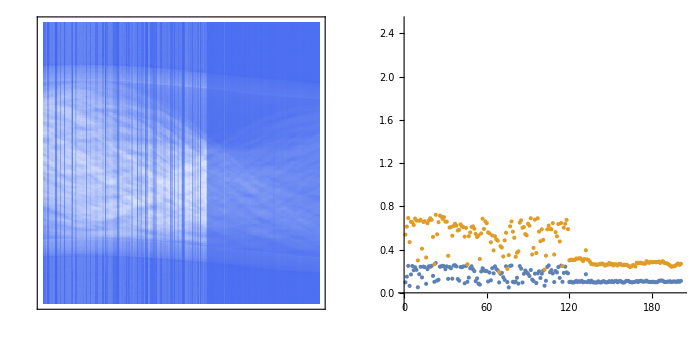

```mathematica
gSino=ArrayPlot[ allSinograms[[165,All,All]], 
PlotRange->{All,All,{-0.1,2.5}},ColorFunction->"TemperatureMap",ClippingStyle->{Black,White},Frame->True];
lineProbe =allSinograms[[165,{30,120},All]];
gLineProbe=ListPlot[lineProbe, PlotRange->{-0.1,2.5}, AxesOrigin->{0,0}];
GraphicsRow[{gSino,gLineProbe},ImageSize->700]
```

### Step 4c. Find best center of rotation using ImagePad and reconstruction of a slice

```mathematica
sinogram= Image[allSinograms[[100,All,All]],"Real"]
```

```mathematica
GraphicsColumn[{ 
 InverseRadon[ImagePad[sinogram,{{0,0},{9,0}},0],numberColumns], 
 InverseRadon[ImagePad[sinogram,{{0,0},{10,0}},0],numberColumns], 
 InverseRadon[ImagePad[sinogram,{{0,0},{11,0}},0],numberColumns], 
 InverseRadon[ImagePad[sinogram,{{0,0},{12,0}},0],numberColumns], 
 InverseRadon[ImagePad[sinogram,{{0,0},{13,0}},0],numberColumns]  }, ImageSize->400]
```

### Step 4d. Shift the sinograms and save as HDF5 files

```mathematica
bestShift = {11,0};
For[indexSlice =1, indexSlice≤numberSlices,indexSlice++,
sinogram= Image[allSinograms[[indexSlice,All,All]],"Real"];
sinogram= ImagePad[sinogram,{{0,0},bestShift},0];
sinogram=ImageData[sinogram,"Real"];
filenameHDF5 = NotebookDirectory[]<>"sinograms/sino_"<>IntegerString[indexSlice,10,4]<>".h5";
Export[filenameHDF5,sinogram,{"Datasets","sinogram"}];
];
```

## Step 5. Reconstruct the sinograms into slices (1 minute)

### Step 5a. Read one sinograms and recontruct into a slice. Test different kernels (poor performance for most kernels, TS 36054 Oct 8, 2012)

```mathematica
filenamesSinograms = FileNames["sino_*",NotebookDirectory[]<>"sinograms/"];
numberSlices = Length[filenamesSinograms];
sinogram=Import[filenamesSinograms[[100]],{"Datasets","sinogram"}];
{numberRays,numberAngles}=Dimensions[sinogram]
sinogram= Image[sinogram,"Real"]
```

```mathematica
sliceRamp = InverseRadon[sinogram,numberRays,numberAngles, "Filter"->(#&)]//ImageAdjust;
sliceRampCosine = InverseRadon[sinogram,Automatic, "Filter"->(#Cos[#Pi]&)]//ImageAdjust;
sliceHann = InverseRadon[sinogram,numberRays, "Filter"->((1+Cos[#Pi])/2&)]//ImageAdjust;
sliceHamming = InverseRadon[sinogram,numberRays, "Filter"->((0.54+0.46 Cos[#Pi])&)]//ImageAdjust;
sliceButterworthOne = InverseRadon[sinogram,numberRays, "Filter"->(Sqrt[1/(1+#^(2×1))]&)]//ImageAdjust;
sliceButterworthThree= InverseRadon[sinogram,numberRays, "Filter"->(Sqrt[1/(1+#^(2×3))]&)]//ImageAdjust;
sliceNone= InverseRadon[sinogram,numberRays, "Filter"->None,"CutoffFrequency"->1]//ImageAdjust;
GraphicsGrid[{{sliceRamp, sliceRampCosine,  sliceHann}, {sliceHamming,  sliceButterworthOne, sliceButterworthThree}, {sliceNone }},ImageSize->700]
```

```mathematica
sliceHann = InverseRadon[sinogram,numberRays, "Filter"->((1+Cos[#Pi])/2&),"CutoffFrequency"->200]//ImageAdjust
```

### Step 5b. Read all sinograms and recontruct into slices

```mathematica
filenamesSinograms = FileNames["sino_*",NotebookDirectory[]<>"sinograms/"];
numberSlices = Length[filenamesSinograms];
sinogram=Import[filenamesSinograms[[1]],{"Datasets","sinogram"}];
{numberColumns,numberRows}=Dimensions[sinogram]
```

```mathematica
For[indexSlice =1, indexSlice≤numberSlices,indexSlice++,
sinogram=Import[filenamesSinograms[[indexSlice]],{"Datasets","sinogram"}];
sinogram=Image[sinogram,"Real"];
slice = InverseRadon[sinogram,numberColumns, "Filter"->(#Cos[#Pi]&)];
slice=ImageData[slice,"Real"];
filenameHDF5 = NotebookDirectory[]<>"slices/slice_"<>IntegerString[indexSlice,10,4]<>".h5";
Export[filenameHDF5,slice,{"Datasets","slice"}];
filenameJPEG= NotebookDirectory[]<>"slices/slice_"<>IntegerString[indexSlice,10,4]<>".jpeg";
Export[filenameJPEG,Image[slice,"Real"]];
];
```

## Step 6. Store all slices into one HDF5 file

### Step 6a. Store all slices into one HDF5 file

```mathematica
filenamesSlices= FileNames["slice_*",NotebookDirectory[]<>"slices/"];
numberSlices = Length[filenamesSlices]
slice=Import[filenamesSlices[[1]],{"Datasets","slice"}];
{numberColumns,numberColumns}=Dimensions[slice]
volume=ConstantArray[0,{numberSlices,numberColumns,numberColumns}];
```

```mathematica
For[indexSlice =1, indexSlice≤numberSlices,indexSlice++,
slice=Import[filenamesSlices[[indexSlice]],{"Datasets","slice"}];
volume[[indexSlice,All,All]]=slice;
];
filenameHDF5 = NotebookDirectory[]<>"bullet_volume_"<>
StringReplace[ToString[{numberSlices,numberColumns,numberColumns}],{" "->""}]<>".h5";
Export[filenameHDF5,volume,{"Datasets","volume"}];
```

### Step 6b. Read the HDF5 file. Calculate statistics of the volume: min, mean, max, and histogram

```mathematica
NotebookDirectory[]
```

```mathematica
filenameHDF5= FileNames["bullet_volume_*",NotebookDirectory[]][[1]]
Import[filenameHDF5]
volume=Import[filenameHDF5, {"Datasets","/volume"}];
```

```mathematica
{Min[volume],Mean[Flatten[volume]],Max[volume]}
```

```mathematica
Histogram[RandomSample[Flatten[volume],10^5],{-5,5,0.05}]
```

### Step 6c. Make a quick 3D graphic (~0.5 minute with MaxPlotPoints→60) (disabled)

```mathematica
(* contourLevels3D={0.2,0.3,0.4,0.5,0.6};
gContour3D=ListContourPlot3D[volume, Contours->contourLevels3D, Mesh->None,AspectRatio->Automatic,BoxRatios->Automatic,Axes->True,
AxesLabel->{Style["rows",FontSize->14],Style["columns",FontSize->14],Style["slices",FontSize->14]},
LabelStyle->Directive[Black,FontSize->14],
PerformanceGoal->"Quality",
ContourStyle->{Directive[Blue,Opacity[0.1],Specularity[White,30]],
Directive[Green,Opacity[0.1],Specularity[White,30]],
Directive[Yellow,Opacity[0.1],Specularity[White,30]],
Directive[Orange,Opacity[0.1],Specularity[White,30]],
Directive[Red,Opacity[0.1],Specularity[White,30]]},
BoundaryStyle->None,
MaxPlotPoints->60,PlotRange->All]
*)
```

### Step 6d. Move the viewpoint around the drawing (can take 10 minutes) (disabled)

```mathematica
(* contourLevels3D={0.2,0.3,0.4,0.5,0.6};
gContour3DNoBox=ListContourPlot3D[volume, Contours->contourLevels3D, Mesh->None,AspectRatio->Automatic,BoxRatios->Automatic,
Axes->False,Boxed->False,
PerformanceGoal->"Quality",
ContourStyle->{Directive[Blue,Opacity[0.02],Specularity[White,30]],
Directive[Green,Opacity[0.02],Specularity[White,30]],
Directive[Yellow,Opacity[0.05],Specularity[White,30]],
Directive[Orange,Opacity[0.1],Specularity[White,30]],
Directive[Red,Opacity[0.3],Specularity[White,30]]},
BoundaryStyle->None,
MaxPlotPoints->90,PlotRange->All] *)
```

```mathematica
(* TableForm[ listViewPoints = Table[{i,{1000*Sin[i*π/180], -1000Cos[i*π/180],-1000}//N},{i,-100,100,20}] ]
interpViewPoints = Interpolation[listViewPoints,InterpolationOrder->1];  *)
```

```mathematica
(* angleList = Range[-100,100,2]; 

For[i=1,i≤Length[angleList],i++,
filenameJPG = NotebookDirectory[]<>"figures/volume_contour3D_"<>IntegerString[i,10,4]<>"deg.jpg";
angle = angleList[[i]];
gReadyToSave =Show[gContour3DNoBox,SphericalRegion->True, ViewVertical->{0,0,1},ViewPoint->interpViewPoints[angle],ImageSize->500];
(* Print[gReadyToSave]; *)
Export[filenameJPG,gReadyToSave,"JPEG","CompressionLevel"->0.05];
] *)
```

```mathematica
(* filenameAllFigures=FileNames[ NotebookDirectory[]<>"figures/volume_contour3D_*.jpg"];
indexMax=Length[filenameAllFigures];
allImages =Table[ Import[filenameAllFigures[[index]] ], {index,3,indexMax}];
Export[ NotebookDirectory[]<>"movie_volume_fly-around.mov", allImages,"FrameRate"->15]  *)
```

### Step 6e. Test Mathematica 9 image tools

```mathematica
filename = FileNames[NotebookDirectory[]<>"bullet_volume_*"][[1]]
```

```mathematica
volume=Import[filename,{"Datasets","volume"}];
Dimensions[volume]
imageVolume = Image3D[volume];
 Clear[volume];
ImageDimensions[imageVolume]
```

```mathematica
Image3D[imageVolume,ColorFunction->"GrayLevelOpacity",Background->Black,Boxed->True]
```

```mathematica
binaryVolume = Binarize[imageVolume,6*FindThreshold[imageVolume]]
```

```mathematica
binaryVolumeVersion2 = MorphologicalBinarize[imageVolume,{4,6}*FindThreshold[imageVolume]]
```

```mathematica
labelVolume = MorphologicalComponents[imageVolume,10FindThreshold[imageVolume]];
Dimensions[labelVolume]
Max[labelVolume]
Colorize[labelVolume]
```

### Step 6f. Use Manipulate to view orthoslices

```mathematica
size = 256;
Manipulate[Grid[{#&/@{Show[Image3DSlices[imageVolume,{s},1][[1]],Graphics[{Red,Line[{{c,0},{c,size}}],Line[{{0,size-r+1},{size,size-r+1}}]}]],
Show[Image3DSlices[imageVolume,{r},2][[1]],Graphics[{Red,Line[{{c,0},{c,size}}],Line[{{0,size-s+1},{size,size-s+1}}]}]],
Show[Image3DSlices[imageVolume,{c},3][[1]],Graphics[{Red,Line[{{r,0},{r,size}}],Line[{{0,size-s+1},{size,size-s+1}}]}]]}}],
{s,1,size,1},{r,1,size,1},{c,1,size,1}]
```

### Step 6g. Save as signed 16-bit integer (int16), little endian, with 20000 scaling factor (

```mathematica
{numberSlices,numberColumns,numberColumns}=Dimensions[volume]
```

```mathematica
filenameRAW = NotebookDirectory[]<>"bullet_"<>
StringReplace[ToString[{numberSlices,numberColumns,numberColumns}],{" "->"",","->"_","{"->"","}"->""}]<>"_int16_le.raw"
```

```mathematica
scaleFactor = 20000;
volumeRaw = Flatten[Round[volume*scaleFactor]];
{Min[volumeRaw],Max[volumeRaw]}
volumeRaw = Map[If[#>(2^15-1),(2^15-1),#] &,volumeRaw];
volumeRaw = Map[If[#<-2^15,-2^15,#] &,volumeRaw];
{Min[volumeRaw],Max[volumeRaw]}
Histogram[RandomSample[volumeRaw,100000]]
```

```mathematica
BinaryWrite[filenameRAW,volumeRaw,"Integer16",ByteOrdering->-1]
```

## Error checking: Compare projections from reconstructed volume with original data (this code not finished)

Dimensions[abs0deg]
Dimensions[volume]

Image[Reverse[Transpose[Reverse[abs0deg, {2}]], {2}], "Real"] // ImageAdjust

Image[Total[volume, {3}], "Real"] // ImageAdjust

Dimensions[ tempAbs = Reverse[Transpose[Reverse[abs0deg, {2}]], {2}] ]
Dimensions[ tempVolume = Total[volume, {3}] ]

indexSlice = 150;
lineProbeAbs = tempAbs[[indexSlice, All]];
gAbs = ListPlot[lineProbeAbs, Joined -> True]

lineProbeVolume = 0.01*tempVolume[[indexSlice, All]];
gVolume = ListPlot[lineProbeVolume];
Show[{gAbs, gVolume}, PlotRange -> All]